```mathematica
ClearAll["Global`*"]
```

q0 Is the initial mortality rate for an organism of mass M
If M is grams, a0 = 0.594 (1.88*10^-8 sec) and b0 = -0.56

```mathematica
q0 = a0*M^b0;
```

α is the Gompertz constant for actuarial aging rate... it is the annual rate of increase in mortality; if M is grams, a1 = 4.45 (1.45*10^-7 sec); b1 = -0.27

```mathematica
α = a1*M^b1;
```

Life expectancy
a2 = 4.04*10^6 seconds gram^-b2; b2 = 0.30

```mathematica
texp = a2*M^b2;
```

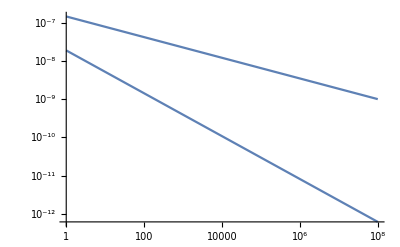

```mathematica
LogLogPlot[{q0,α}/.{a0->1.88*10^-8,b0->-0.56,a1->1.45*10^-7,b1->-0.27},{M,1,10^8}]
```

The Gompertz Equation: number of surviving from previous year... so t is in a population’s lifetime, and n(t) is the number of individuals surviving from year to year.

```mathematica
n = n0*Exp[q0/α*(1-Exp[α*t])];
```

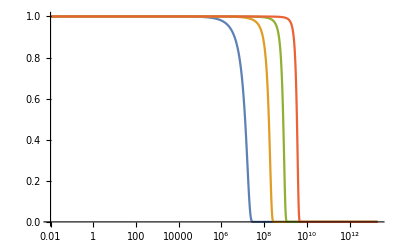

```mathematica
masses={1,10^3,10^5,10^7};
Show[
Table[LogLinearPlot[n/.{a0->1.88*10^-8,b0->-0.56,a1->1.45*10^-7,b1->-0.27,n0->1,M->masses[[i]]},{t,0.01,20000000000000},PlotRange->All,PlotStyle->ColorData[97,i]],{i,1,4}]
]
```

```mathematica
mortratetime = FullSimplify[-D[n,t]*(1/n)]
```

a0 ⅇ^(a1 M^b1 t) M^b0

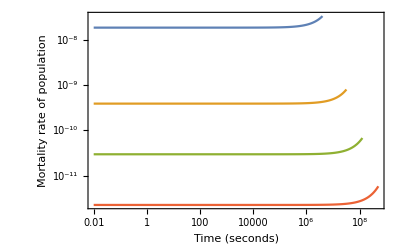

```mathematica
With[{a0=1.88*10^-8,b0=-0.56,a1=1.45*10^-7,b1=-0.27,a2=4.04*10^6,b2=0.30},
masses={1,10^3,10^5,10^7};
tend = a2*masses^b2;
Show[
Table[LogLogPlot[a0 ⅇ^(a1 M^b1 t) M^b0/.M->masses[[i]],{t,0.01, tend[[i]]},PlotRange->All,PlotStyle->ColorData[97,i],Frame->True,FrameLabel->{"Time (seconds)","Mortality rate of population"}],{i,1,4}]
]
]
```

```mathematica
avgmortrate = (1/texp)*Integrate[mortratetime,{t,0,texp}]
```

(a0 (-1+ⅇ^(a1 a2 M^(b1+b2))) M^(b0-b1-b2))/(a1 a2)

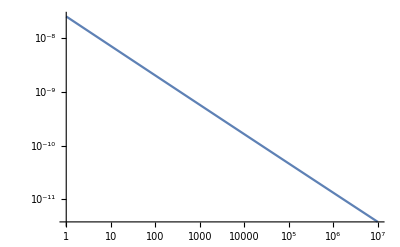

```mathematica
LogLogPlot[avgmortrate/.{a0->1.88*10^-8,b0->-0.56,a1->1.45*10^-7,b1->-0.27,a2->4.04*10^6,b2->0.30},{M,1,10^7}]
```

Altering expected mortality patterns via external predation/hunting

IMPORTANT... if we expect hunting to impact the aging rate, it should impact α
...if we expect hunting to impact the initial mortality rate, it should impact q0
For now it might just be easier to assume that it impacts q0... if it impacts α, increasing α for a particular Mass means that there are fewer older age classes (predators are extracting the older prey). If q0 is higher, I think this means that there is larger uniform mortality

Here is a very simplistic one... we have the scalings of intial mortality rate q0... and scalings for the annual rate of increase in mortality α with just an added mass independent term.

```mathematica
With[{a0=1.88*10^-8,b0=-0.56,a1=1.45*10^-7,b1=-0.27},
q0 = a0*M^b0;
q0adj = a0*M^b0;
(*q0 Is the initial mortality rate for an organism of mass M*)
α=a1*M^b1;
αadj=a1*M^b1 ;
(*α is the Gompertz constant for actuarial aging rate... it is the annual rate of increase in mortality*)
Manipulate[
LogLogPlot[{q0,α,a0*M^b0+ξ},{M,1,10^8},Frame->True,FrameLabel->{"Mass (g)","Life history mortality rates (1/s)"}],{ξ,0,0.000001}]
]
```

If we want an additional mass-dependent mortality... we could use the predation window defined by Rohr to capture the additional mortality within a particular link-probability window... so that gives us pr(link) = f(M)... then predationmortality = ξf(M) for a particular predator size M_p

```mathematica
nsurvivors = n0*Exp[q0/α*(1-Exp[α*t])]
```

ⅇ^(((1-ⅇ^(t α)) q0)/α) n0

```mathematica
nsurv[q0_,α_,n0_] :=ⅇ^(((1-ⅇ^(t α)) q0)/α) n0
```

```mathematica
mortcohort=(-D[nsurvivors,t]*(1/(nsurvivors)))
```

ⅇ^(t α) q0

```mathematica
mortcorhortrate[q0_,α_] :=ⅇ^(t α) q0
```

```mathematica
avgmort=(1/texp)* Integrate[mortcohort,{t,0,texp}]
```

((-1+ⅇ^(texp α)) q0)/(texp α)

```mathematica
avgmortrate[{q0_,α_,texp_}]:=((-1+ⅇ^(texp α)) q0)/(texp α)
```

Here is the average mortality rate as a function of 
[q0: initial mortality rate (1/s); α: actuarial mortality rate (1/s); texp: expected lifespan (s)]

```mathematica
avgmortrate[{ a0*M^b0, a1*M^b1, a2*M^b2}]
```

(a0 (-1+ⅇ^(a1 a2 M^(b1+b2))) M^(b0-b1-b2))/(a1 a2)